EPToolbox package

## Initialization

This package includes a smal suite of supporting functions for varied applications.

To get things going, load the package.

```mathematica
Needs["EPToolbox`"]
```

(Note that this is possible because the package has been installed, by adding the line $Path=Join[$Path,{“/home/episanty/Work/CQD/Project/Code/EPToolbox/EPToolbox”}] to the file /home/episanty/.Mathematica/Kernel/init.m.)

## Testing

```mathematica
Quit
```

```mathematica
NSolve[{1+(1-Sin[t])^2==0.1Sin[tt],2+(1-Sin[tt])^2==0.01Cos[t]}, {t,tt}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.639625-1.00689 ⅈ,tt→0.546377+1.27521 ⅈ},{t→0.639625+1.00689 ⅈ,tt→0.546377-1.27521 ⅈ},{t→0.725756-1.06149 ⅈ,tt→0.543716-1.2739 ⅈ},{t→0.725756+1.06149 ⅈ,tt→0.543716+1.2739 ⅈ},{t→2.41547-1.06152 ⅈ,tt→0.544452+1.27946 ⅈ},{t→2.41547+1.06152 ⅈ,tt→0.544452-1.27946 ⅈ},{t→2.50234-1.00692 ⅈ,tt→0.541816-1.27817 ⅈ},{t→2.50234+1.00692 ⅈ,tt→0.541816+1.27817 ⅈ}}

```mathematica
(results=FindComplexRoots[
{1+(1-Sin[t])^2==0.001Sin[tt],1+(1+Sin[tt])^2==0.001Cos[t]}
, {t,-2ⅈ,2π+2ⅈ},{tt,0,2π+2ⅈ}
,SeedGenerator->RandomSobolComplexes
,Seeds->100
,Tolerance->0.01
])//Sort//Length
ListPointPlot3D[
Flatten[{ReIm[t],Re[tt]}]/.results
,ImageSize->450
,PlotRange->{{0,π},{-2,2},{π,2π}}
,PlotStyle->PointSize[Large]
]
```

8

-Graphics3D-

```mathematica
RandomSobolComplexes
```

```mathematica
Solve
```

## Functions

### FindComplexRoots

This is a function to solve numerically (mainly trascendental) equations on the complex plane. It is documented in depth in http://mathematica.stackexchange.com/a/57821.

Its main usage is as follows:

```mathematica
Quit
```

```mathematica
?FindComplexRoots
Options[FindComplexRoots]
?Seeds
?SeedGenerator
?Tolerance
```

FindComplexRoots[e1==e2, {z, zmin, zmax}] attempts to find complex roots of the equation e1==e2 in the complex rectangle with corners zmin and zmax.

FindComplexRoots[{e1==e2, e3==e4, …}, {z1, z1min, z1max}, {z2, z2min, z2max}, …] attempts to find complex roots of the given system of equations in the multidimensional complex rectangle with corners z1min, z1max, z2min, z2max, ….

{AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision,Seeds→50,SeedGenerator→RandomComplex,Tolerance→Automatic,Verbose→False}

Seeds is an option for FindComplexRoots which determines how many initial seeds are used to attempt to find roots of the given equation.

SeedGenerator is an option for FindComplexRoots which determines the function   used to generate the seeds for the internal FindRoot call. Its value can be RandomComplex, RandomNiederreiterComplexes, RandomSobolComplexes, DeterministicComplexGrid, or any function f such that f[{zmin, zmax}, n] returns n complex numbers in the rectancle with corners zmin and zmax.

Tolerance is an option for various numerical options which specifies the tolerance that should be allowed in computing results.

Some simple examples:

```mathematica
FindComplexRoots[1+(1-Sin[t])^2==0.1 t, {t,-2ⅈ,2π+2ⅈ}]
```

{{t→2.46095+0.963404 ⅈ},{t→0.709879-1.06182 ⅈ},{t→2.46095-0.963404 ⅈ},{t→0.709879+1.06182 ⅈ}}

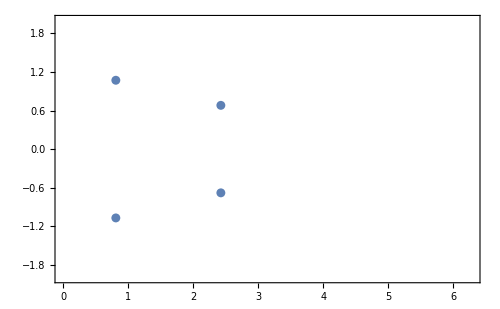

```mathematica
ListPlot[
{Re[t],Im[t]}/.FindComplexRoots[1+(1-Sin[t])^2== 0.3t, {t,-2ⅈ,2π+2ⅈ}]
,Frame->True
,ImageSize->500
,PlotRange->{{0,2 π},{-2,2}}
]
```

### Benchmarking suite for FindComplexRoots

FindComplexRoots works probabilistically, by randomly seeding points in the given rectangle and then using descent methods to find roots. This means that if not enough seeds are tried (i.e. the Seeds option is too low) then the function may behave erratically and return an incomplete (and varying) set of roots. To deal with this behaviour, the following is a benchmarking suite to help determine the seeding characteristics required by each equation for consistent behaviour.

#### Timings and generation of the benchmarks

```mathematica
Monitor[
Table[
{seedGenerator,AbsoluteTiming[
benchmark[seedGenerator]=Flatten[Table[
{seedNumber,Length[#⟦2⟧],#⟦1⟧}&[AbsoluteTiming[
FindComplexRoots[
(1+(1-Sin[t])^2)(1+(1+Sin[t])^2)==0.01t,{t,-2ⅈ,2π+2ⅈ}
,Tolerance->Automatic,Seeds->seedNumber,SeedGenerator->seedGenerator
]
]]
,{seedNumber,1,30},{repetition,100}
],1];
]⟦1⟧}
,{seedGenerator,{RandomComplex,RandomSobolComplexes,RandomNiederreiterComplexes,DeterministicComplexGrid}}]
,{seedGenerator,seedNumber,repetition}]//TableForm
```

RandomComplex | 35.12634
RandomSobolComplexes | 35.99328
RandomNiederreiterComplexes | 36.16267
DeterministicComplexGrid | 64.18689

#### Number of roots found vs number of seeds

Dot diameter proportional to the number of repetitions that gave that number of roots.

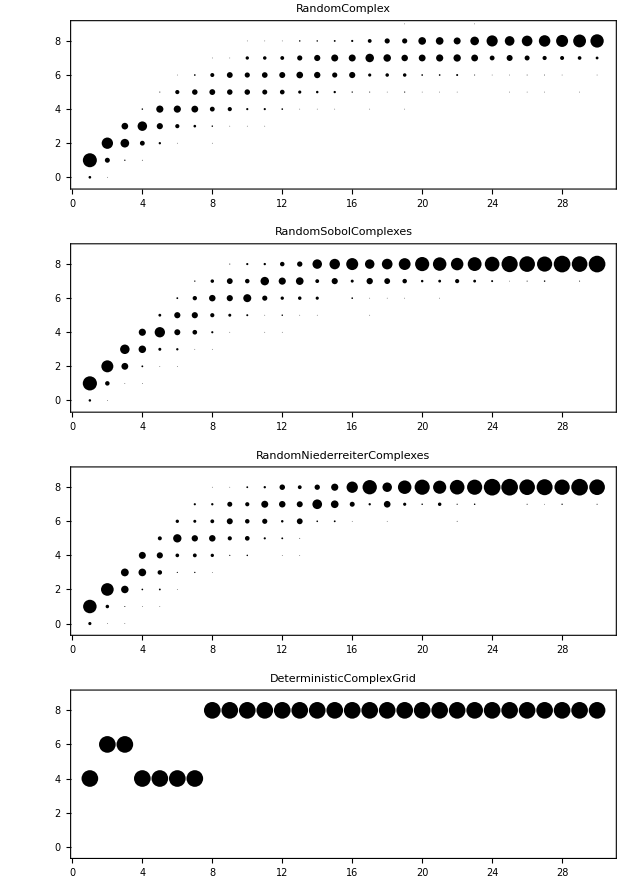

```mathematica
GraphicsColumn[
Table[
Show[
Graphics[
{PointSize[0.0002 #2],Point[#1]}]&@@@Tally[
benchmark[seedGenerator]⟦All,{1,2}⟧
]
,Frame->True
,ImageSize->600
,AspectRatio->1/3
,PlotRange->{{.5,30.5},{-0.5,9}}
,PlotLabel->ToString[seedGenerator]
]
,{seedGenerator,{RandomComplex,RandomSobolComplexes,RandomNiederreiterComplexes,DeterministicComplexGrid}}]
]
```

#### More detailed statistics on the distribution of roots found

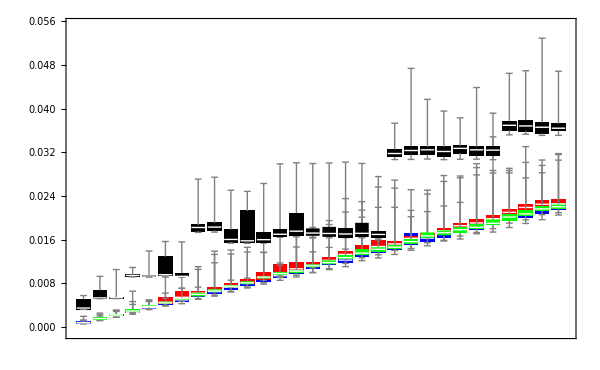

```mathematica
Show[
Table[
BoxWhiskerChart[
SplitBy[
benchmark[seedGenerator]⟦All,{1,3}⟧
,First]⟦All,All,2⟧
,ImageSize->600
,PlotRangePadding->None
,ChartStyle->seedGenerator/.{
RandomComplex->Blue,RandomSobolComplexes->Red,RandomNiederreiterComplexes->Green,DeterministicComplexGrid->Black
}
]
,{seedGenerator,{RandomComplex,RandomSobolComplexes,RandomNiederreiterComplexes,DeterministicComplexGrid}}]
]
```

### Quasirandom complex number generators.

The performance of FindComplexRoots can be increased, as shown above, by using quasirandom numbers instead of pure random selections. (Pseudo)random numbers tend to bunch up, in the plane, which increases the chances of roots being missed or repeated. To remedy this, it is often beneficial to use low-discrepancy quasirandom number generators, which are more evenly distributed on the complex plane.

```mathematica
?RandomComplex
?RandomSobolComplexes
?RandomNiederreiterComplexes
?DeterministicComplexGrid
```

RowBox[{"RandomComplex", "[", "]"}] gives a pseudorandom complex number with real and imaginary parts in the range 0 to 1.
RowBox[{"RandomComplex", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["z", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["z", "TI"], StyleBox["max", "TI"]]}], "}"}], "]"}] gives a pseudorandom complex number in the rectangle with corners given by the complex numbers SubscriptBox[StyleBox["z", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["z", "TI"], StyleBox["max", "TI"]].
RowBox[{"RandomComplex", "[", SubscriptBox[StyleBox["z", "TI"], StyleBox["max", "TI"]], "]"}] gives a pseudorandom complex number in the rectangle whose corners are the origin and SubscriptBox[StyleBox["z", "TI"], StyleBox["max", "TI"]].
RowBox[{"RandomComplex", "[", RowBox[{StyleBox["range", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives a list of StyleBox["n", "TI"] pseudorandom complex numbers.
RowBox[{"RandomComplex", "[", RowBox[{StyleBox["range", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives an SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]]×SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]×… array of pseudorandom complex numbers.

RandomSobolComplexes[{zmin, zmax}, n] generates a low-discrepancy Sobol sequence of n quasirandom complex numbers in the rectangle with corners zmin and zmax.

RandomNiederreiterComplexes[{zmin, zmax}, n] generates a low-discrepancy Niederreiter sequence of n quasirandom complex numbers in the rectangle with corners zmin and zmax.

DeterministicComplexGrid[{zmin, zmax}, n] generates a grid of about n equally spaced complex numbers in the rectangle with corners zmin and zmax.

#### Distribution of the different (pseudo/quasi)random number generators on the complex plane

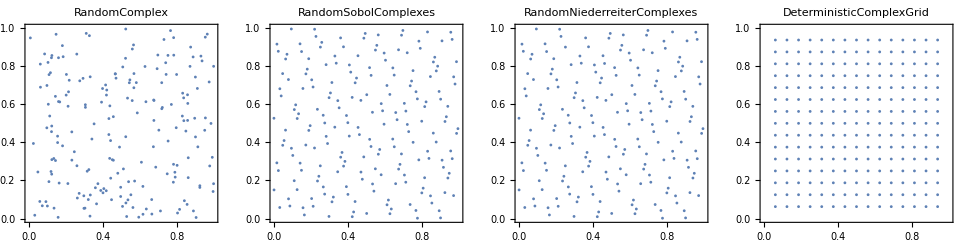

```mathematica
GraphicsRow[
Table[
ListPlot[
{Re[#],Im[#]}&/@seedGenerator[{0,1+ⅈ},200]
,Frame->True
,PlotRange->{{0,1},{0,1}}
,AspectRatio->1
,PlotLabel->ToString[seedGenerator]
,ImageSize->220
]
,{seedGenerator,{RandomComplex,RandomSobolComplexes,RandomNiederreiterComplexes,DeterministicComplexGrid}}]
]
```

#### Timings statistics

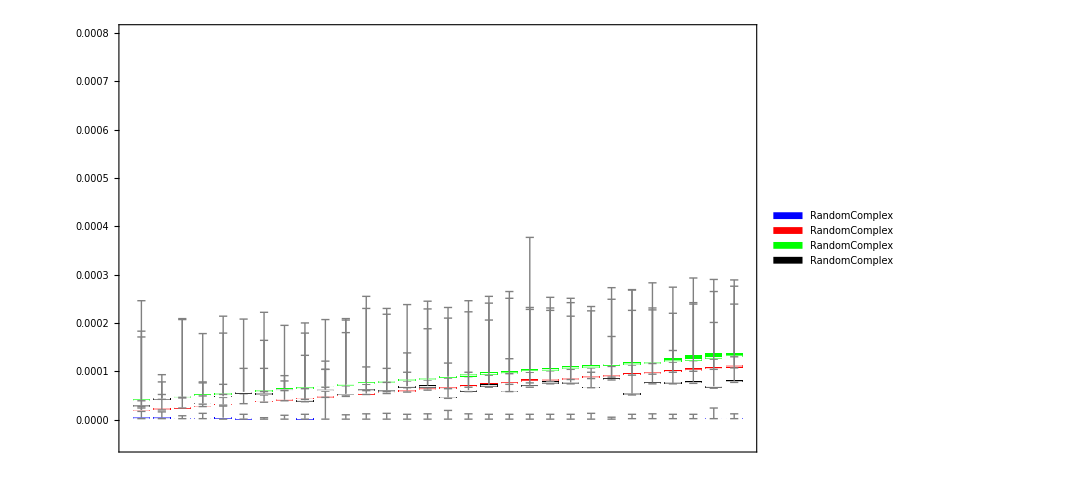

```mathematica
Show[
Monitor[Table[
BoxWhiskerChart[
SplitBy[
Table[
{n,First[AbsoluteTiming[seedGenerator[{0,1+ⅈ},n]]]}
,{n,1,30},{repetitions,500}]
,First]⟦All,All,All,2⟧
,ImageSize->800
,PlotRange->{0,0.004}
,PlotRangePadding->None
,ChartStyle->(seedGenerator/.{
RandomComplex->Blue,RandomSobolComplexes->Red,RandomNiederreiterComplexes->Green,DeterministicComplexGrid->Black
})
,ChartLegends->{RandomComplex,RandomSobolComplexes,RandomNiederreiterComplexes,DeterministicComplexGrid}
]
,{seedGenerator,{RandomComplex,RandomSobolComplexes,RandomNiederreiterComplexes,DeterministicComplexGrid}}]
,{seedGenerator,n,repetitions}]
,PlotRange->{-0.00005,0.0008}
]
```

### cleanContourPlot

This function cleans up automatically generated contour plots. Generically, a contour plot is made of a Polygon with a vast number of vertices in its interior, which are not necessary and only slow the plot down - including a large use of CPU when the mouse hovers above it, which is definitely unwanted. (In addition, these polygons can give rise to white edges inside each contour when printed to pdf, which is also undesirable.) This function changes such Polygons to FilledCurve constructs which no longer contain the unwanted mid-contour points.

This function was written by Szabolcs Horvát (http://mathematica.stackexchange.com/users/12/szabolcs) and was originally posted at http://mathematica.stackexchange.com/a/3279 under a CC-BY-SA license.

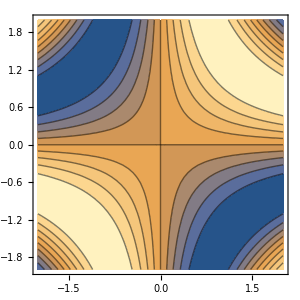
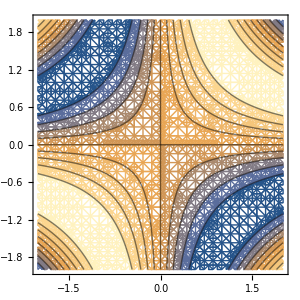
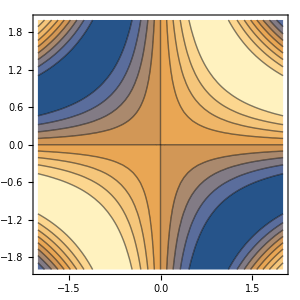
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{#,#/.Polygon->Line,cleanContourPlot[#],cleanContourPlot[#]/.Polygon->Line}]&@ContourPlot[
Sin[x y]
,{x,-2,2},{y,-2,2}
,ImageSize->300,PlotRangePadding->None
]
```

### profileDynamics

This function produces a profiling suite for any dynamics constructs, which can be used to see which parts of a Dynamic application take up the most processing time and calls.

This function was written by Rui Rojo (http://mathematica.stackexchange.com/users/109/rojo)and was originally posted at http://mathematica.stackexchange.com/a/8047 under a CC-BY-SA license.

```mathematica
profileDynamics[
DynamicModule[
{a=0.1,point={1,1}},
Column[{
Slider[Dynamic[a]],
LocatorPane[
Dynamic[point],
Dynamic[
Show[
ContourPlot[
Sin[a x y],{x,-5,5},{y,-5,5}
,ImageSize->300,PlotRangePadding->None
],
Graphics[Line[{{0,0},Dynamic[point]}]]
]
]
],
Dynamic[point]
}]
]
]
```